ImplicitRegion::bcond: Null should be a Boolean combination of equations, inequalities, and Element statements.

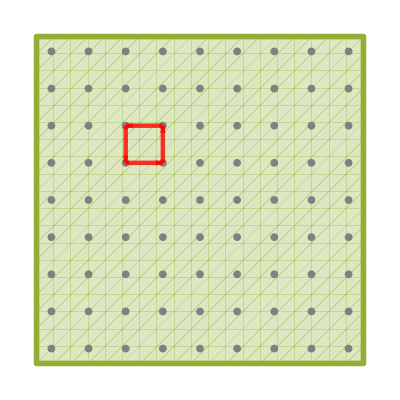

```mathematica
Show[{RegionPlot[{,,-1≤x≤2&&-1≤y≤2},{x,-.05,1.05},{y,-.05,1.05},Frame->None,FrameLabel->{Subscript[k, x],Subscript[k, y]},BoundaryStyle->Thickness[.01]],Graphics[{Gray,PointSize[.014],Point[Flatten[Outer[{#1,#2}&,Range[0.,1.,.125],Range[0.,1.,.125]],1]]}],Graphics[{Opacity[.8],Red,Thickness[.008],Arrowheads[.04],Arrow/@{{{.25,.625},{.375,.625}},{{.375,.625},{.375,.75}},{{.375,.75},{.25,.75}},{{.25,.75},{.25,.625}}}}]}]
```